# PX4514: Volleyball Setter Model

## Pawel Kaniowski and Sonke Wohler

## Initialisation and Model Definitions

This Group of instructions should be executed automatically upon opening the Notebook. 
It serves as the initialisation, defining constants and functions required by the Model

```mathematica
CleanSlate[];ClearAll["Global`*"]; 
(* only the combination of these commands seems to completely clear the kernel *)
```

### Constants for the Model

Note that constants, while near exclusively static values, may be defined as functions at times due to the limitations set out by the Mathematica programming language.

#### Coordinate System specs

We laid a coordinate system over the playing field in order to describe player positions independent of their position in the rotation.

```mathematica
(* boundaries for the coordinate system *)
minX=1 ; maxX=13;
minY=1 ; maxY=9;
(* boundaries of the allowed playing field inside the coordinate system (players can contact the ball outside this area but only without toughing the ground) *)
startX=3 ; endX=11;
startY=1 ; endY=9;
(* translate coordinates to a decimal between 0 and 1 *)
getXScale[x_]=x/maxX;
getYScale[y_]=1-(y/maxY); (* y coordinates are reverse between our representation and mathematica image coordinates *)
```

#### Constants specific to each position

Here we used function definitions rather than lists in order to start indices from 0.
0 refers to the setter independent of their position, and in the case of attack to a “Dump” where the setter goes straight to the attack without setting to a position, while indices above 0 directly describe the player that is being set to.
player numbers describe their position inside the rotation, in accordance with volleyball standards.

```mathematica
(* ideal position to set from *) 
idealCoordinates[0]={8,1}; 
(* ideal position for player at position p to contact the ball at *)
idealCoordinates[1]={10,3}; 
idealCoordinates[2]={11,1};
idealCoordinates[3]={7,1};
idealCoordinates[4]={3,1};
idealCoordinates[5]={4,3};
idealCoordinates[6]={7,3};
```

```mathematica
(* basic assumed bias of a "Dump"*)
positionBias[0]=0.4;
(* basic assumed bias for a player at position p to attack successfully *)
positionBias[1]=0.4;
positionBias[2]=0.5;
positionBias[3]=0.3;
positionBias[4]=0.4;
positionBias[5]=1.0;
positionBias[6]=0.5;
(* front court players have to be scored slightly higher to reflect their proximity to the net and higher set rate, despite having lower success rates *)
```

```mathematica
(* the setter's coordinates are dynamically defined by setterPosition *)
positionCoordinates[0]:=setterCoordinates;
(* the coordinates that a player at position p is assumed to start from when the ball is served *)
positionCoordinates[1]={11,6};
positionCoordinates[2]={9,1};
positionCoordinates[3]={9,1};
positionCoordinates[4]={3,1};
positionCoordinates[5]={4,2};
positionCoordinates[6]={8,2};
```

```mathematica
(* the coordinates that positions have as they are usually displayed *) 
displayCoordinates[1]={10,7};
displayCoordinates[2]={10,2};
displayCoordinates[3]={7,2};
displayCoordinates[4]={4,2};
displayCoordinates[5]={4,7};
displayCoordinates[6]={7,7};
```

```mathematica
(* determines whether the setter is allowed to set to a position or not *)
positionIsValid[0]:=setterCoordinates[[2]]≤1; (* "Dump" is only feasable very close to the net *)
positionIsValid[1]=True;(**)
positionIsValid[2]=True;(**)
positionIsValid[3]=True;(**)
positionIsValid[4]=True;(**)
positionIsValid[5]=False;(* 5 is usually libero, a player that does not attack *)
positionIsValid[6]=True; (**)
```

```mathematica
(**)
scaleXList=Table[getXScale[displayCoordinates[i][[1]]],{i,6}];
scaleYList=Table[getYScale[displayCoordinates[i][[2]]],{i,6}];
```

#### Scale quantities by their expected maximum

Lastly, throughout the model it proved useful to use relative values by scaling factors and terms relative to their maximum possible value, resulting in a fraction i.e.

```mathematica
scaleFactor[max_,quant_]:=1-(quant/max);
```

```mathematica
maxDistance=EuclideanDistance[{maxX,maxY},{startX,startY}];
```

```mathematica
(* The maximum difficulty that can be assigned by 'positionSetDifficulty'*)
maxSetDifficulty=0.9*maxDistance^2;
```

```mathematica
maxPressure=23;
```

```mathematica
maxRun=EuclideanDistance[positionCoordinates[1],{minX,minY}];
```

```mathematica
maxDifficulty=1;
```

```mathematica
(* the assumed maximum number of plays  *)
maxSettings=100;
```

```mathematica
(* for final positionScores *)
 maxPositionScore=maxPressure*(1+1);
```

### Functional Decelerations

The functional specifications of the Model begin here. These translate to Mathematical functions as also described in the Project Report.

#### Functions without Parameters

These functions are unspecific to any particular player and change only when game parameters change e.e. when a point is scored.

```mathematica
(* the amount of pressure the players feel due to the game state *)
pressure:=Max[(oponentsPoints-ownPoints)*Min[Max[ownPoints,oponentsPoints]/25,1] ,0]+1;
```

```mathematica
(* how far the setter is from the ideal setting position *)
distanceFromIdeal:=EuclideanDistance[setterCoordinates,idealCoordinates[0]];
```

```mathematica
(* how comfortably the setter could reach the ball from their position *)
distanceToRun:=EuclideanDistance[positionCoordinates[setterPosition],setterCoordinates];
```

```mathematica
(* whether the setter is in front court (=True) or back court (=False) *)
setterIsFrontCourt:=MemberQ[{2,3,4},setterPosition];
```

```mathematica
(* describes the difficulty the setter has to contact the ball, reducing the quality of the set *)
easeOfSet:=scaleFactor[maxDistance,distanceToRun]*scaleFactor[maxDistance,distanceFromIdeal];
```

#### Parameterized Functions based on Player Positions

These Functions evaluate and usually score some properties of individual players on the playing field.

```mathematica
(* converts positionIsValid[p] to a number *)
positionValidityFactor[p_Integer]:=If[positionIsValid[p]  && p≠setterPosition,1,0];
```

```mathematica
(* how far the setter would have to throw to set to position p *)
distanceToThrow[p_Integer ]:=EuclideanDistance[ setterCoordinates,idealCoordinates[p]];
```

```mathematica
(* score position p by how likely the setter is to set to it well *)
setToScore[p_Integer]:=scaleFactor[maxSetDifficulty,distanceToThrow[p]];
```

```mathematica
(* score a position p by how likely the player is to attack successfully *)
attackerScore[p_Integer]:=scaleFactor[maxDifficulty,positionBias[p]];
```

```mathematica
(* score a position p by how likely the setter may be to set to it *)
positionScore[p_]:= positionValidityFactor[p]*pressure*(setToScore[p]+easeOfSet*attackerScore[p]);
```

#### Top Level

These Functions are intended to ease usage of the Model or allow atomisation of it.

```mathematica
(* score all positions based on the already defined input values *)
calculateAllScores:=listOfScores=Table[positionScore[p],{p,0,6}];
```

```mathematica
(* use preveously calculated scores and convert them to percentage values *)
convertScoresTopercentages:=
percentageScores=listOfScores/Total[listOfScores];
```

```mathematica
(* set input values *)
setInputs[ownPointsIn_Integer,oponentsPointsIn_Integer,setterPositionIn_Integer,setterCoordinatesIn_List]:=
ownPoints=ownPointsIn;oposingPoints=oponentsPointsIn;remainingSets=remainingSetsIn;setterCoordinates=setterCoordinatesIn;
```

### Initialise with some Default Input Variables

These are examples of the required inputs that are used as default in case the functions are called without these having been initialized. Hence any unexpected outputs or errors are cause by bugs or failure to run initialisation entirely.

```mathematica
(* the current score for our team *)
ownPoints=0;
```

```mathematica
(* the current score for the opposing team *)
oponentsPoints=0;
```

```mathematica
(* the position inside the rotation that the setter is in *)
setterPosition=1;
```

```mathematica
(* the coordinates on the field that the setter contacts the ball at *)
setterCoordinates={9,2};
```

```mathematica
(* initialise listOfScores as well *)
calculateAllScores;
```

### Preparing Images and similar for Visualisation

These images may be used for visualisation purposes in the corresponding section.

```mathematica
fieldImage=-Graphics-;
```

```mathematica
excelFieldImage=-Graphics-;
```

```mathematica
fieldDisplayImage=ImageResize[fieldImage,ImageDimensions[excelFieldImage]];
```

```mathematica
displayScores:=calculateAllScores;
convertScoresTopercentages;
displayImage=fieldDisplayImage;
For[i=1,i<7,i++,
text=Interpreter["PercentFraction"][percentageScores[[i+1]]];
graphs=Graphics[ Text[ text ] ];
scale={ scaleXList[[i]],scaleYList[[i]] };
displayImage=ImageCompose[displayImage,graphs,Scaled[scale]];
];
```

## Short Description of the Model

The following variables are used to run the Model:

```mathematica
ownPoints=5(* how many points we scored so far *);
oponentsPoints=10  (* this puts us 5 points behind *);
setterPosition=2 (* the position within the player rotation that the setter is currently occupying *);
setterCoordinates= {8,1} (* the playing field coordinates on which the setter has come into contact with the ball *);
```

The Model calculates a score for each player by the position they occupy, for example player 3:

```mathematica
positionScore[3]
```

3.27713

This scores the likelihood of the setter to set the ball to this position based on the difficulty to do so and the chances that this will lead to scoring a point against the opponent.

```mathematica
?? positionScore
```

Global`positionScore

positionScore[p_]:=positionValidityFactor[p] pressure (setToScore[p]+easeOfSet attackerScore[p])

Positions that cannot be set to, or that never are in game, are scored with 0 by the `positionValidityFactor`

Furthermore, `setToScore` describes the difficulty for the setter to set to a particular position.

`easeOfSet` describes how difficult it was for the setter to still contact the ball and perform a successful set. The assumption being that the harder this was the more the setter will focus on choosing a position that they will still be able to successfully set to, and reducing the relevance of the `attackerScore`.

The `attackerScore` simply describes a bias to choose certain positions. For the most part positions closer to the net are more promising as they give the opponent less time to react, while the centre position does so extremely well as long as the setter is close enough.

Lastly, the `pressure` a player is under is set based on the current state of the game.

You can calculate the scores for all players by executing `calculateAllScores`.

```mathematica
calculateAllScores
```

{3.1063,3.06797,0.,3.27713,3.03855,0.,2.89161}

The first return value refers to something called “Dump”, when the setter does not set to any other player but instead attacks directly.
Then the players are scored in order from 1 to 6. Note that position 5 is not allowed (typically) and that the setter cannot set to themselves.

## Example Comparisons to Real World Data

```mathematica
(* a Dataset from a real match to compare the model to *)
ownPointsList={2,2,3,3,3,6,8,9,10,11,14,15,17,18,18,19,19,20,23,23,23,25};
oponentsPointsList={2,3,4,4,5,6,7,8,9,10,12,13,14,15,16,16,16,17,21,23,24,25};
setterPositionList={1,1,6,6,6,5,4,3,2,1,5,4,3,2,2,1,1,1,5,5,5,3};
setterCoordinateList={{5,3},{6,5},{7,1},{7,2},{8,5},{7,3},{6,5},{10,3},{5,1},{7,3},{8,2},{8,2},{9,5},{7,1},{6,2},{8,4},{8,2},{12,6},{5,3},{7,3},{7,4},{10,2}};
setToList={2,4,3,4,2,2,4,1,3,2,0,6,1,4,4,4,2,6,4,2,4,3};
(* the set is 22 entries long *)
```

```mathematica
getFromLists[i_Integer]:=ownPoints=ownPointsList[[i]];
oponentsPoints=oponentsPointsList[[i]];
setterPosition=setterPositionList[[i]];
setterCoordinates=setterCoordinateList[[i]];
```

```mathematica
positionScoreList=Range[22];
For[i=1,i<23,i++,
getFromLists[i];
calculateAllScores;
convertScoresTopercentages;
positionScoreList[[i]]=percentageScores;
];
```

```mathematica
positionScoreList
```

{{0.,0.33173,0.,0.343276,0.,0.,0.324995},{0.,0.33173,0.,0.343276,0.,0.,0.324995},{0.,0.33173,0.,0.343276,0.,0.,0.324995},{0.,0.33173,0.,0.343276,0.,0.,0.324995},{0.,0.33173,0.,0.343276,0.,0.,0.324995},{0.,0.33173,0.,0.343276,0.,0.,0.324995},{0.,0.33173,0.,0.343276,0.,0.,0.324995},{0.,0.33173,0.,0.343276,0.,0.,0.324995},{0.,0.33173,0.,0.343276,0.,0.,0.324995},{0.,0.33173,0.,0.343276,0.,0.,0.324995},{0.,0.33173,0.,0.343276,0.,0.,0.324995},{0.,0.33173,0.,0.343276,0.,0.,0.324995},{0.,0.33173,0.,0.343276,0.,0.,0.324995},{0.,0.33173,0.,0.343276,0.,0.,0.324995},{0.,0.33173,0.,0.343276,0.,0.,0.324995},{0.,0.33173,0.,0.343276,0.,0.,0.324995},{0.,0.33173,0.,0.343276,0.,0.,0.324995},{0.,0.33173,0.,0.343276,0.,0.,0.324995},{0.,0.33173,0.,0.343276,0.,0.,0.324995},{0.,0.33173,0.,0.343276,0.,0.,0.324995},{0.,0.33173,0.,0.343276,0.,0.,0.324995},{0.,0.33173,0.,0.343276,0.,0.,0.324995}}

## Plotting

```mathematica
displayImage
```

-Graphics-

## Debugging and Testing Section

This section should be removed before submission

```mathematica
ownPointsList={2,2,3,3,3,6,8,9,10,11,14,15,17,18,18,19,19,20,23,23,23,25};
oponentsPointsList={2,3,4,4,5,6,7,8,9,10,12,13,14,15,16,16,16,17,21,23,24,25};
setterPositionList={1,1,6,6,6,5,4,3,2,1,5,4,3,2,2,1,1,1,5,5,5,3};
setterCordinateList={{5,3},{6,5},{7,1},{7,2},{8,5},{7,3},{6,5},{10,3},{5,1},{7,3},{8,2},{8,2},{9,5},{7,1},{6,2},{8,4},{8,2},{12,6},{5,3},{7,3},{7,4},{10,2}};
setToList={2,4,3,4,2,2,4,1,3,2,0,6,1,4,4,4,2,6,4,2,4,3};
```

```mathematica
number
text
```

0.241

24.0676 %

```mathematica
ImageCompose[fieldDisplayImage,Graphics[Text[attackerScore[1]]],Scaled[{getXScale[10],getYScale[7]}]]
```

-Graphics-

```mathematica
setterCoordinates={10,3};
setterPosition=5;
easeOfSet*1.0
Table[attackerScore[p]*1.0,{p,0,6}]
Table[setToScore[p]*1.0,{p,0,6}]
calculateAllScores
```

0.409059

{0.6,0.6,0.5,0.7,0.6,0.,0.5}

{0.980837,1.,0.98485,0.975572,0.950677,0.95935,0.979675}

{0.,1.24544,1.18938,1.26191,1.19611,0.,1.1842}

```mathematica
calculateAllScores; percentageScores
```

{0.,0.0859468,0.,0.0880426,0.0830236,0.,0.0814629}

```mathematica
listOfScores
```

{0.,3.95355,0.,4.04996,3.81909,0.,3.74729}

```mathematica
percentageScores
```

{0.,0.253923,0.,0.260115,0.245287,0.,0.240676}

```mathematica
percentageScores
```

{0.,0.,0.242964,0.26504,0.249033,0.,0.242964}

0

{10/13,10/13,7/13,4/13,4/13,7/13}

{2/9,7/9,7/9,7/9,2/9,2/9}

10/13

2/9

{10/13,2/9}

Scaled[{10/13,2/9}]

-Graphics-

ImageCompose::posinv: Invalid position specification in Scaled[{List,List}].

ImageCompose::imginv: Expecting an image or graphics instead of ….

ImageCompose::posinv: Invalid position specification in Scaled[{List,List}].

ImageCompose::imginv: Expecting an image or graphics instead of ….

ImageCompose::posinv: Invalid position specification in Scaled[{List,List}].

General::stop: Further output of ImageCompose::posinv will be suppressed during this calculation.

ImageCompose::imginv: Expecting an image or graphics instead of ….

General::stop: Further output of ImageCompose::imginv will be suppressed during this calculation.

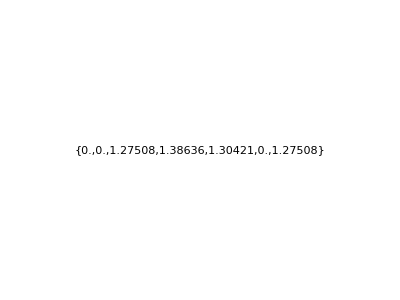
ImageCompose[ImageCompose[ImageCompose[ImageCompose[ImageCompose[ImageCompose[ImageCompose[ImageCompose[ImageCompose[-Graphics-,-Graphics-,Scaled[{List,List}]],-Graphics-,Scaled[{10/13,2/9}]],-Graphics-,Scaled[{10/13,7/9}]],-Graphics-,Scaled[{7/13,7/9}]],-Graphics-,Scaled[{4/13,7/9}]],-Graphics-,Scaled[{4/13,2/9}]],-Graphics-,Scaled[{7/13,2/9}]],-Graphics-,Scaled[{10/13,2/9}]],-Graphics-,Scaled[{10/13,2/9}]]

```mathematica
scaleXList
scaleYList
scaleXList[[1]]
scaleYList[[1]]
scale={ scaleXList[[1]],scaleYList[[1]] }
Scaled[scale]
graphs=Graphics[ Text[ listOfScores[[2]] ] ]
displayImage=ImageCompose[displayImage,graphs,Scaled[scale]]
```